```mathematica
ParametricPlot[{Sin[x]^-1,Cos[x]^-1}, {x,0,4π}]
```

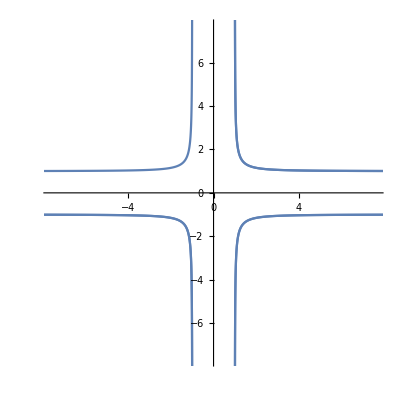
```mathematica
-Graphics-[Sin[x],Cos[x],x, {x,0,2π}]
```

```mathematica
ParametricPlot3D[{Sin[x],Cos[x],x},{x,0,4 π},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

### Astroid

The astroid was first discussed by Johann Bernoulli in 1691-92. It also appears in Leibniz’s correspondence of 1715. It is sometimes called the tetracuspid for the obvious reason that it has four cusps.

The astroid only acquired its present name in 1836 in a book published in Vienna. It has been known by various names in the literature, even after 1836, including cubocycloid and paracycle.

```mathematica
https://mathshistory.st-andrews.ac.uk/Curves/Astroid/
```

```mathematica
a:= 3
```

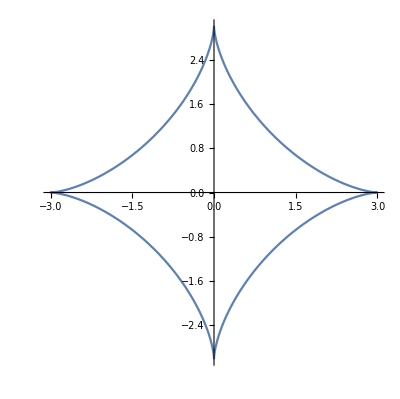

```mathematica
ParametricPlot[ {a*Cos[t]^3,a*Sin[t]^3} ,{t, 0 ,2π}]
```

```mathematica
ParametricPlot3D[ {a*Cos[t]^3,a*Sin[t]^3, Cos[t]} ,{t, 0 ,2π}]
```

-Graphics3D-

### Fermat’s Spiral

This spiral was discussed by Fermat in 1636.

For any given positive value of θ there are two corresponding values of rrr, one being the negative of the other. The resulting spiral will therefore be symmetrical about the liney=−xy = -xy=−x as can be seen from the curve displayed above. 

https://mathshistory.st-andrews.ac.uk/Curves/Fermats/

```mathematica
a := 4
```

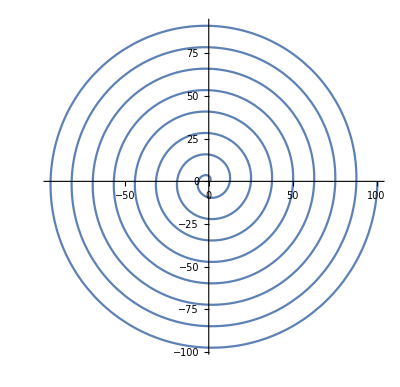

```mathematica
ParametricPlot[{√a*θ*Cos[ θ],√a*θ*Sin[ θ]},{θ, 0, 16 π}]
```